```mathematica
J[x_]:=BesselJ[1,x];
Y[x_]:=BesselY[1,x];
Y[0.000000]
```

ComplexInfinity

```mathematica
b[x_,k_]:= (J[x/k] - x/k*J'[x/k])/(Y[x/k] - x/k*Y'[x/k]);
```

```mathematica
b[10,1.0*10^12]
```

```mathematica
Solve[b[x]-b[Exp[12*π]*x] == 0,x,Reals]
```

```mathematica
Mpl = (2435/1000)*10^18;
```

```mathematica
kr[Λ_]:= Log[Mpl/Λ]/π;
```

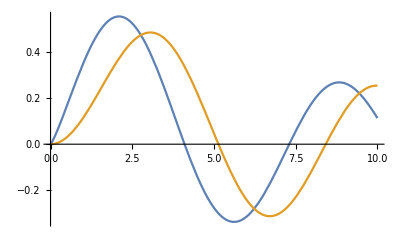

```mathematica
Plot[{BesselJ[1.2,x],BesselJ[2,x]},{x,0,10}]
```

```mathematica
(* s = 2(4) for vectors (fermions)*)
```

```mathematica
Subscript[m, even][s_,n_,k_,Λ_]:= (n +(s/2) - 3/4)*π*k*Exp[-π*kr[Λ]];
Subscript[m, odd][s_,n_,k_,Λ_]:= (n +(s/2) - 1/4)*π*k*Exp[-π*kr[Λ]];
```

```mathematica
Subscript[m, even][2,1,2.0*10^15,10^3]
```

3.22545

```mathematica
Subscript[m, odd][2,1,(2.435*10^18),10^3]
```

5497.79

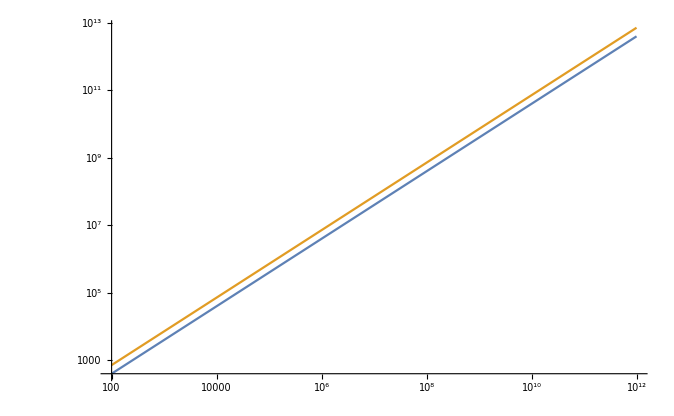

```mathematica
LogLogPlot[{Subscript[m, even][2,1,2.435*10^18,x],Subscript[m, even][4,1,2.435*10^18,x]},{x,100,10^12}]
```

```mathematica
f[n_,k_,Λ_,y_]:= Exp[y]*(BesselJ[1,Subscript[m, even][2,n,k,Λ]*Exp[y]] + b[Subscript[m, even][2,n,k,Λ],k]*BesselY[1,Subscript[m, even][2,n,k,Λ]*Exp[y]]);

Plot[f[1,10^17,10^12,y],{y,0,10}]
```

-Graphics-

```mathematica
Ln[100]
```

```mathematica
Log[100]
```

```mathematica
Log[100]
```

Log[100]

```mathematica
N[Log[100],4]
```

```mathematica
4.605170185988091368`4./π
```

1.466

```mathematica
Log[100]/.Simplify
```

ReplaceAll::reps: {Simplify} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Log[100]/.Simplify

```mathematica
19/33
```

```mathematica
N[19/33]
```

0.575758